```mathematica
matrix[sx_,sy_,ϕ_] =2 {{1/sx^2, -Tan[ϕ]/sx^2},{-Tan[ϕ]/sx^2,2/sy^2+(2/sy^2+1/sx^2)Tan[ϕ]^2}}
```

{{2/sx^2,-(2 Tan[ϕ])/sx^2},{-(2 Tan[ϕ])/sx^2,2 (2/sy^2+(1/sx^2+2/sy^2) Tan[ϕ]^2)}}

```mathematica
tol[sx_,sy_,ϕ_]:=1/Sqrt[reconstructEllipse[2/sx^2,2 (2/sy^2+(1/sx^2+2/sy^2) Tan[ϕ]^2),-2 Tan[ϕ]/sx^2,1][[1]]]
```

```mathematica
tolEllipse[{xM_,yM_,ϕM_},sx_,sy_,R_]:=ellipse[{xM,yM},2/sx^2,2 (2/sy^2+(1/sx^2+2/sy^2) Tan[ϕM]^2),-2 Tan[ϕM]/sx^2,R]
```

```mathematica
tolEllipse[{{xM_,yM_},ϕM_},sx_,sy_,R_]:=ellipse[{xM,yM},2/sx^2,2 (2/sy^2+(1/sx^2+2/sy^2) Tan[ϕM]^2),-2 Tan[ϕM]/sx^2,R]
```

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

```mathematica
Convert[SpeedOfLight  150 Pico Second, Meter]/4//N
```

0.0112422 Meter

```mathematica
Convert[SpeedOfLight  150 Pico Second, Meter]/Sqrt[2]//N
```

0.0317978 Meter

```mathematica
3.0/Sqrt[tol[11,32,0 Degree][[1]]]
```

{23.3345,48.}

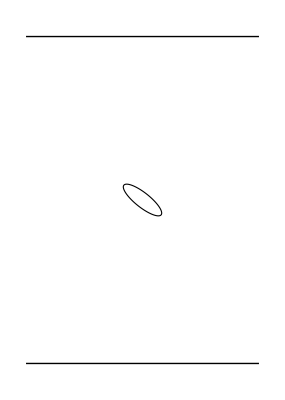

```mathematica
Graphics[
{Line[{{-250,-350},{250,-350}}],Line[{{-250,350},{250,350}}],
tolEllipse[{0,0,-45 Degree},11,32,3]}
]
```

```mathematica
T=matrix[11,32,45 Degree]
```

{{2/121,-2/121},{-2/121,377/15488}}

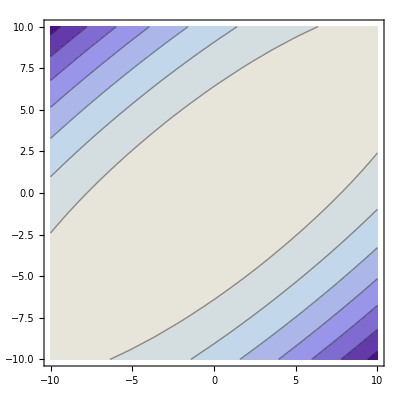

```mathematica
ContourPlot[-{x,y}.T.{x,y},{x,-10,10},{y,-10,10}]
```

```mathematica
reconstructEllipse[T[[1,1]],T[[2,2]],T[[1,2]],1]
```

{{0.0374194,0.00345094},2.24016}

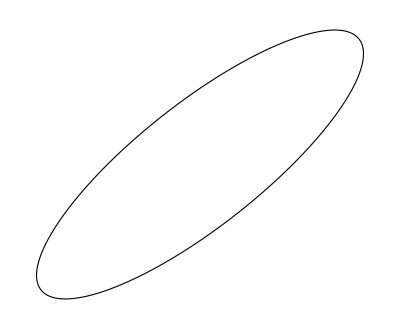

```mathematica
tolEllipse[{0,0,45 Degree },11,32,1]//Graphics
```

```mathematica
tol[11,32,45 °]
```

{{0.0374194,0.00345094},-2.24016}